```mathematica
InDir=NotebookDirectory[]<>"input/";
OutDir=NotebookDirectory[]<>"output/";
SpecDir=NotebookDirectory[]<>"spec/";

INSIDE="INSIDE";
OUTSIDE="OUTSIDE";

MTBPLow="MTBPLow";
MTBPLH="MTBPLH";
Naritaka="Naritaka";

RwCONST="RwCONST";
RwBOL="RwBOL";
RwDAMP="RwDAMP";
RwLOR="RwLOR";

SolarMass=2*10^30; (*kg*)
G=6.7*10^-11;(*m3⋅kg−1⋅s−2*)
LightVelo=3*10^8;(*(m s-1)*)
lp=1.6*10^-35;(*m*)
α= (G *Mass)/LightVelo^3; (* Mω/(2 π*α) =f，t/M *α = true time in second, here Mω means the  horizon axis value in the spectrum *)

(*Use Naritaka Oshita's code to calculate |R_{BH}|^2 , χ=0.69,  Lambda = 1/100000  *)
TRef69sm2=Import[StringJoin[InDir,"RBHs-2chi0.69.dat"],"Table"];
refl69m=Interpolation[TRef69sm2];

RwdampDataV02Chi69=Import[StringJoin[InDir,"RwdampV0.2Chi0.69M50N200.dat"],"Table"];
RwdampV02Chi69=Interpolation[RwdampDataV02Chi69];

(*Ringdown *)
RingdownPaniData=Import[StringJoin[InDir,"ringdown_Pani.dat"],"Table"];
RdPani=Interpolation[RingdownPaniData];
(*ZH: top-right in Fig 4. of ShuoXin 2105.12313 *)
ZHXinData=Import[StringJoin[InDir,"ZHXin.csv"]];
ZHXin=Interpolation[ZHXinData];
(* Z(1) : top-right of Fig .10   of ShuoXin 2105.12313*)
LorZ1Data=Import[StringJoin[InDir,"XinFig10TopZ1.csv"]];
LorZ1=Interpolation[LorZ1Data];


(*---------------------------*)

displayLaTeX[string_]:=DisplayForm[ToBoxes@TraditionalForm@ToExpression[string,TeXForm,HoldForm]];

(*for s=-2, l=2, m=-2 ,n=0 *)
ωR2m2[χ_]:=0.2938+0.0782*(1-χ)^1.3546;
ωI2m2[χ_]:=(-ωR2m2[χ])/(2 (1.6700+0.4192  * (1-χ)^1.47));

(*Quasinormal modes of black holes and black branes :formular(96)
There is a typo in (96). There should be a minus before 0.499. 
See Table VIII in reference [10]:gr-qc/0512160.
 *)
(*for s=-2, l=m=2 ,n=0 *)
ωR22[χ_]:=1.5251-1.1568*(1-χ)^0.1292;
ωI22[χ_]:=(-ωR22[χ])/(2 (0.7+1.4187   *(1-χ)^-0.499));
mΩ[m_,χ_]:=(m* χ)/(2*(1+Sqrt[1-χ^2]));
kH[{m_,χ_},ω_]:=ω-mΩ[m,χ];
Δr[r_,χ_]:=r^2+χ^2-2 r;
rp[χ_]:=1+ Sqrt[1-χ^2] ;
TH[χ_]:=Module[{r},Abs[D[Δr[r,χ],r]/(4 π*(r^2+χ^2))//.{r-> rp[χ]}]   ];

(*----------------------------------*)
RingD[{t0_,Ap_,Ac_,ϕp_,ϕc_},χ_,ω_]:=Module[{ ϕ,α1,α1p,α1c,α2p,α2c,ωQNM,rd },
ωQNM=ωR22[χ]+I*ωI22[χ];
α1=I*Exp[-I(ϕ+t0*ωQNM)];
α1p=α1/.{ϕ->ϕp};
α1c=α1/.{ϕ->ϕc};
α2p=-Conjugate[α1p];
α2c=-Conjugate[α1c];

rd=Exp[I ω t0]/(2 √(2 π))((α1p*Ap-α1c*Ac)/(ω-ωQNM)+(α2p*Ap+α2c*Ac)/(ω+Conjugate[ωQNM]))
];

RingDω[ω_]:=RingD[{t0,Ap,Ac,ϕp,ϕc},χ,ω];
RingDf[f_]:=RingD[{t0,Ap,Ac,ϕp,ϕc},χ,2 π*α*f];

Zeff[{m_,χ_},ω_]:=Module[{M,a,rp,k,λ0, λ1,λ2, λ,l,s,Order3,ϵ,d,d2,C2,FoutP,FinM,Ze},
Order3=0;
l=2;
s=-2;

M=1;
rp=1+ Sqrt[1-χ^2] ;
a=χ*M;
k=kH[{m,χ},ω];
λ0=l(l+1)-s(s+1);

λ1=-2m(1+s^2/(l(l+1)));
H[l_]:=(2(l^2-m^2)(l^2-s^2)^2)/((2l-1)l^3(2l+1));
λ2=1+(H[l+1]-H[l]-1);


λ=λ0+χ*ω * λ1+χ^2 ω^2 λ2 +Order3;

(*λ=((l-s)*(l+s+1)+χ^2*ω^2-2*χ*m*ω +some)/.{some->0,l->2,s->-2}; *)

ϵ=(rp-M)/(4M*rp);
rp=1+ Sqrt[1-χ^2] ;

C2=λ^4+4 λ^3+λ^2(-40 a^2 ω^2+40a*m*ω+4)+48a*λ*ω(a*ω+m)+144 ω^2(a^4 ω^2-2 a^3*m*ω+a^2 m^2+M^2);
FoutP=1/(2 ω^2);

FinM=(128ω(2M*rp)^5 k(k^2+4*ϵ^2)(k^2+16*ϵ^2))/C2;

Ze=Sqrt[Abs[FinM/FoutP]]*  Sqrt[Abs[1/refl[ω]-1]] * ZHXin[ω];
Ze
]
(*----------------------------------*)


LenBol[m_,χ_,ω_]:=Module[{γ,k,len},
(*position of wall*)
γ=1;
k=ω-mΩ[m,χ]; 
len= (Log[γ *  Abs[k] ]-92)/(2*π *TH[χ]);
(*92 is the transformation factor between Log[k ] and Log[hf/E_Pl], TFac*)
len
];

LenPl[Mass_,χ_]:=Module[{η,len},
(*position of wall*)
η=2;
len=-η   * Log[ (G* Mass)/(lp * LightVelo^2)] *(1.+(1.-χ^2)^(-1/2)) ;
len 
];


Rbol[m_,χ_,TFac_,ω_]:=Module[{k,γ,Rb},
γ=1.;
k=ω-mΩ[m,χ]; 
Rb=Exp[- Abs[k]/(2*TH[χ]*TFac)]       
(*for the dimensional analysis, see the note echonote. *)
];




Rdamp[{m_ ,Mass_,χ_,OVERLOPT_},{Vi_,αbar4_,ζ_,Rw_}, ω_]:=Module[{x , mΩ,η,len,Overl,LNorm,Rd},
(*original value*)
mΩ=(m  χ)/(2*(1+Sqrt[1-χ^2]));
len=Abs[LenPl[Mass,χ]];
LNorm=NIntegrate[1./9.  * 1./(1.+0.03  x^2),{x,0,len}];
If[(OVERLOPT==True),
   (Overl=NIntegrate[1./(9.*LNorm)  * 1./(1.+0.03  x^2) *(4 Rw*(Sin[(ω-mΩ) *x ])^2 + (Rw-1)^2)/(1.+Rw^2),{x,0,len} ]  ),
    (Overl=1)];
Rd=Exp[-4 Pi Vi  ζ  (1+(8 Pi *(ω-mΩ)* ζ  )^2/αbar4  )^-1  *  Overl]

(*--Use interpolation for χ=0.69: For
RwParDamp69V02=<|"RwOPT"->RwDAMP,"m"->2,"Mass"->50 *SolarMass,"χ"->χ,"OVERLOPT"->True,"Vi"->0.2, "αbar4"->0.01,"ζ"->2.5,"Rw"->1|>;
----*)
(*Rd=Abs[RwdampV02Chi69[ω]]*)
];

Rlor[{m_,χ_},{A_,Γ_},ω_]:=(A*I*Γ)/((ω-mΩ[m,χ])+I*Γ);

Rwall[Par_,ω_]:=Module[{Rw},
Which[Par["RwOPT"]==RwCONST,(Rw=Par["RwVal"]),
           Par["RwOPT"]==RwBOL,( Rw=Rbol[   Par["m"], Par["χ"],Par["TFac"],ω  ]),
           Par["RwOPT"]==RwDAMP,(Rw=Rdamp[  {Par["m"],Par["Mass"],Par["χ"],Par["OVERLOPT"]},{Par["Vi"],Par["αbar4"],Par["ζ"],Par["Rw"]}  ,ω]),
	Par["RwOPT"]==RwLOR,(Rw=Rlor[{Par["m"],Par["χ"]},{Par["A"],Par["Γ"]},ω])
];

Rw * Exp[I π * 6/5]
];


SetAttributes[RwallData,HoldAll];
RwallData[{nEcho_,Mass_,RwPar_,χ_},{ωrange_,Rwdata_}]:=Module[{Time,Δω,δω,NP},
Δω=2.; (*sample interval*)
(*Sampling params*)
Time =nEcho*2 * Abs[LenPl[Mass,χ]];
δω=  (2  Pi)/Time ;
NP=2 Floor[0.5  Floor[Δω/δω ]]+1;
ωrange=  δω *(Range[NP]-Floor[NP/2]-1);
Rwdata=Table[Abs[Rwall[RwPar,ω]],{ω,ωrange}];
]

(*----------------------;*)
Reff[m_,χ_,RwPar_,ω_]:=Module[{Mass,k,x0},
(*with phase Exp[-2 I k x0]*)
Mass=50 *SolarMass; (*default for planck length *)
k=ω-mΩ[m,χ];
x0=If[
RwPar["RwOPT"]==RwBOL,N[LenBol[m,χ,ω]],
N[ LenPl[Mass,χ]]]; 
Rwall[RwPar,ω]*  Exp[-2 I k x0]*  Sqrt[refl[ω]]
]

Zp[{LL_,m_},{t0_,Ap_,Ac_,ϕp_,ϕc_},{Mass_,RwPar_,δ_,χ_},{RBHOPT_,nEcho_,DIRE_},ω_]:=Module[  {L,M,rp,rm,a,ϵ,ωR,ωI,k,γ,ξ,ζ,RBHlf,GH,RBH,ωQNM,ϕ,α1,α1p,α1c,α2p,α2c,ωR22,ωI22,ZBHp,x0,Mi,seri,Rw,σ,Zp},
M=1;
ωR22=1.5251-1.1568*(1-χ)^0.1292;
ωI22=-ωR22/(2 (0.7+1.4187   *(1-χ)^(-0.499)));
ωR=ωR22;
ωI=ωI22;

L=LL*M;
rp=M(1+√(1-χ^2));
rm=M(1-√(1-χ^2));
a=χ*M;
ϵ=√(1-χ^2)δ^2/(4 rp^2);

k=ω-(m*a)/(2 M rp);
γ=rm/rp;
ξ=1+√(1-χ^2);
ζ=(ⅈ (2 ω M-m √γ) (γ+1) ξ)/(γ-1);

GH=1/2(rp-rm)/(rp^2+a^2);  (*surface gravity*)
RBHlf=(-8 M k  ⅇ^((ζ(γ-1))/(γ+1))(2 M k-ⅈ (γ-1))/(γ-1)^2((-M (γ-1) ξ)/L)^(ζ(γ-1))   ((16 k^2 M^2)/(γ-1)^2+1) Gamma[-2+ζ] Gamma[-1-ζ] (1800 ⅈ Gamma[-2-ζ]+(ω M (γ-1) ξ)^5 Gamma[3-ζ]))/(Gamma[-2-ζ] Gamma[3-ζ] (1800 ⅈ Gamma[-2+ζ]+(ω M (γ-1) ξ)^5 Gamma[3+ζ]));
RBH=Which[RBHOPT==MTBPLow,RBHlf,
                    RBHOPT==MTBPLH,RBHlf*(Exp[(-2 π ωR)/GH]+1)/(Exp[(2 π(Abs[ω]-ωR))/GH]+1),
                   RBHOPT==Naritaka,Sqrt[refl[ω]]];

ωQNM=ωR+I*ωI;
α1=I*Exp[-I(ϕ+t0*ωQNM)];
α1p=α1/.{ϕ->ϕp};
α1c=α1/.{ϕ->ϕc};
α2p=-Conjugate[α1p];
α2c=-Conjugate[α1c];

ZBHp=Exp[I ω t0]/(2 √(2 π))((α1p*Ap-α1c*Ac)/(ω-ωQNM)+(α2p*Ap+α2c*Ac)/(ω+Conjugate[ωQNM]));

x0=If[
RwPar["RwOPT"]==RwBOL,N[LenBol[m,χ,ω]],
N[ LenPl[Mass,χ]]]; 

(*Outside should use RBH_outside, not the same as RBH_inside*)
Mi=Which[DIRE==INSIDE,1,DIRE==OUTSIDE,(1-1/(Abs[RBH])^2)];
Rw=Rwall[RwPar,ω];
seri=Block[{i,Ref,sum=0},
                       Ref=RBH*Rw*Exp[-2 I k x0];
                        For[i=1, i<=nEcho,i++, 
                              sum+= Ref^i           ];    
                       sum] ;

Zp=N[ZBHp*  Mi*seri  ]
];

SetAttributes[ZpHt,HoldAll];
ZpHt[{LL_,m_},{t0_,Ap_,Ac_,ϕp_,ϕc_},{Mass_,RwPar_,δ_,χ_},{RBHOPT_,nEcho_,DIRE_},{ωrange_,Zpdata_,Trange_,htdata_}]:=Module[{Time,Δω,δω,NP},
Δω=2.; (*sample interval*)
(*Sampling params*)
Time =nEcho*2 * Abs[LenPl[Mass,χ]];
δω=  (2  Pi)/Time ;
NP=2 Floor[0.5  Floor[Δω/δω ]]+1;
(* The least NP in the form of 2^i+1 with Δω *)
(*NP=Block[{i,n}, For[i=5,i<50,i++,   n=2^i+1;  If[n>Δω/(2 Pi) Time,Break[]]; ];   n  ];  *)
ωrange=  δω RotateLeft[(Range[NP]-Floor[NP/2]-1),Floor[NP/2]];
If[(RBHOPT==MTBPLH || RBHOPT==MTBPLow),   
           (Zpdata=Table[Zp[{LL,m},{t0,Ap,Ac,ϕp,ϕc},{Mass,RwPar,δ,χ},
           {RBHOPT,nEcho,DIRE},ω],{ω,ωrange}]/.Indeterminate->0)];
If[RBHOPT==Naritaka,   
          (Zpdata=Table[Zp[{LL,m},{t0,Ap,Ac,ϕp,ϕc},{Mass,RwPar,δ,χ},
         {RBHOPT,nEcho,DIRE},ω],{ω,ωrange}]/.Indeterminate->0)];

Zpdata=ReplacePart[Zpdata,{1->0}];
Trange=Range[0,Time,Time/(NP-1)];
htdata=InverseFourier[Zpdata];
];

ZpdataXin[N_,ωrangeN_]:=Module[{ω,FName,ZpdataXinN},
ZpdataXinN=Transpose[{ωrangeN, LorZ1[ω]/Abs[Reff[2,69/100,RwParL,ω]]*   Sum[Reff[2,69/100,RwParC69, ω]^i,{i,1,N}]/.{ω->ωrangeN}}];
FName=StringJoin[OutDir,"w1XinN",ToString[N],".dat"];
Export[FName,   ZpdataXinN];
ZpdataXinN
]

(*--------------------*)
LL=1;
M=1;
Mass=50 *SolarMass;
m=2;
t0=0;
Ap=1;
Ac=0;
ϕp=0;
ϕc=0;
(* δ=10^-7 M;  not used*)

χ=69/100;  (*mΩ=0.4*)
refl[ω_]:=refl69m[ω];
```

Generate the modulus of reflectivity of the wall for the Damping model:  
-Graphics-
 Need to use the original value other than interpolation value in the function Rdamp

```mathematica
χ=69/100; 
nEchoRw=20;  (*higher resolution for larger nEchoRw*)

RwParDamp69V02=<|"RwOPT"->RwDAMP,"m"->2,"Mass"->50 *SolarMass,"χ"->χ,"OVERLOPT"->True,"Vi"->0.2, "αbar4"->0.01,"ζ"->2.5,"Rw"->1|>;
RwParDamp69V1=<|"RwOPT"->RwDAMP,"m"->2,"Mass"->50 *SolarMass,"χ"->χ,"OVERLOPT"->True,"Vi"->1, "αbar4"->0.01,"ζ"->2.5,"Rw"->1|>;

RwallData[{nEchoRw,Mass,RwParDamp69V02,χ},{ωrange,RwdataV02}]
RwallData[{nEchoRw,Mass,RwParDamp69V1,χ},{ωrange,RwdataV1}]

Export[StringJoin[OutDir,"RwdampV0.2Chi0.69M50N",ToString[nEchoRw],".dat"],Transpose[{ωrange,RwdataV02}]];
Export[StringJoin[OutDir,"RwdampV1Chi0.69M50N",ToString[nEchoRw],".dat"],Transpose[{ωrange,RwdataV1}]];
```

Plot   ,  where  for χ=0.69.  Interpolation is used for the damping model.

15

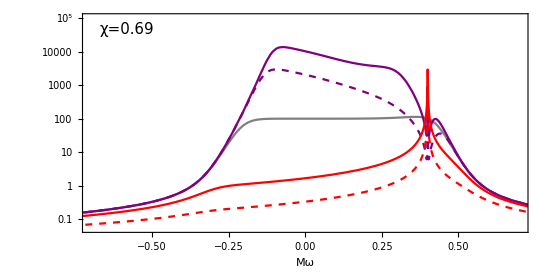

.1e

```mathematica
χ=69/100;  (*mΩ=0.4*)
RwParBolT10Chi69=<|"RwOPT"->RwBOL,"m"->2,"TFac"->10,"χ"->χ|>;
RwParBolT2Chi69=<|"RwOPT"->RwBOL,"m"->2,"TFac"->2,"χ"->χ|>;

RwdampV02Chi69=Interpolation[RwdampDataV02Chi69];

RwdampDataV1Chi69=Import[StringJoin[InDir,"RwdampV1Chi0.69M50N200.dat"],"Table"];
RwdampV1Chi69=Interpolation[RwdampDataV1Chi69];

FS=15
FigLogReff=LogPlot[{
Abs[1/Log[Abs[0.99*Sqrt[refl[ω]]]]],
Abs[1/Log[Abs[RwdampV02Chi69[ω]*Sqrt[refl[ω]]]]],
Abs[1/Log[Abs[RwdampV1Chi69[ω]*Sqrt[refl[ω]]]]],
Abs[1/Log[Abs[Rwall[RwParBolT10Chi69,ω]*Sqrt[refl[ω]]]]],
Abs[1/Log[Abs[Rwall[RwParBolT2Chi69,ω]*Sqrt[refl[ω]]]]]
  },{ω,-0.9,0.9},
Axes->{True,False},
Frame->True,
FrameTicksStyle->Black,
FrameLabel->{ Style["Mω",FontSize->FS,Black],Style["",FontSize->FS,Black]},
FrameStyle->Thickness[0.0019],
PlotRange->{{-0.7,0.7},{0,10^5}},
PlotStyle->{{Gray},{Purple},{Purple,Dashed},{Red},{Red,Dashed}},
PlotLegends->Placed[{"","","","",""},{0.15,0.58}],
LabelStyle->Directive[FontSize->FS],
GridLines->{{mΩ[2,χ],ωR22[χ]},None},GridLinesStyle->Directive[Black,Dashed,Thickness[0.0025]],
Epilog->Text[Style["χ=0.69",FS],Scaled[{0.1,0.93}]],
AspectRatio->0.5,
ImageSize->550]
(*Export[StringJoin[OutDir,"LogReffChi0.69.pdf"],FigLogReff]*).1e
```

Generate spectra for 4 models with nEcho=200. Note that  ZpdataXin (infalling particle model)  has used ωrangeC thus can not do calculation independently.
The spectra are given by-Graphics-,  where , except for infalling particle model where  is given by arxiv 2105.12313  .
(use interpolation function RwdampV02Chi69 in function Rdamp would be much  faster for χ=0.69 in damping model)

```mathematica
RwParC69=<|"RwOPT"->RwCONST,"RwVal"->0.99|>;
RwParDamp69V02=<|"RwOPT"->RwDAMP,"m"->2,"Mass"->50 *SolarMass,"χ"->χ,"OVERLOPT"->True,"Vi"->0.2, "αbar4"->0.01,"ζ"->2.5,"Rw"->1|>;
RwParB10=<|"RwOPT"->RwBOL,"m"->2,"TFac"->10,"χ"->χ|>;  
RwParL=<|"RwOPT"->RwLOR,"m"->2,"χ"->χ,"A"->0.25,"Γ"->0.15|>;

nEcho=20;

ZpHt[{LL,m},{t0,Ap,Ac,ϕp,ϕc},{Mass,RwParC69,δ,χ},{"Naritaka",nEcho,"INSIDE"},{ωrangeC,ZpdataInC,TrangeC,htdataInC}];
Export[StringJoin[OutDir,"w1specM50Rw0.99Chi0.69N",ToString[nEcho],".dat"],Transpose[{ωrangeC,ZpdataInC}]];

ZpHt[{LL,m},{t0,Ap,Ac,ϕp,ϕc},{Mass,RwParB10,δ,χ},{"Naritaka",nEcho,"INSIDE"},{ωrangeB10,ZpdataInB10,TrangeB10,htdataInB10}];
Export[StringJoin[OutDir,"w1specM50RbolT10Chi0.69N",ToString[nEcho],".dat"],Transpose[{ωrangeB10,ZpdataInB10}]];

ZpHt[{LL,m},{t0,Ap,Ac,ϕp,ϕc},{Mass,RwParDamp69V02,δ,χ},{"Naritaka",nEcho,"INSIDE"},{ωrangeD02,ZpdataInD02,TrangeD02,htdataInD02}];
Export[StringJoin[OutDir,"w1specM50RdV0.2Chi0.69N",ToString[nEcho],".dat"],Transpose[{ωrangeD02,ZpdataInD02}]];

ZpdataXin[nEcho,ωrangeC];
```

InterpolatingFunction::dmval: Input value {0.789625} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.789986} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.790347} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Plot spectra for 4 models:

```mathematica
ZpdataCN200=ToExpression[Import[StringJoin[SpecDir,"w1specM50Rw0.99Chi0.69N200.dat"],"Table"]];
ZpdataD02N200=ToExpression[Import[StringJoin[SpecDir,"w1specM50RdV0.2Chi0.69N200.dat"],"Table"]];
ZpdataB10N200=ToExpression[Import[StringJoin[SpecDir,"w1specM50RbolT10Chi0.69N200.dat"],"Table"]];
ZpdataXinN200=ToExpression[Import[StringJoin[SpecDir,"w1XinN200.dat"],"Table"]];

FS=15;
FigSpec69=ListPlot[  { 
RotateRight[ZpdataCN200/.{a_,b_}->{a,Abs[b]},  Floor[Length[ZpdataCN200]/2]   ],
RotateRight[ZpdataD02N200/.{a_,b_}->{a,Abs[b]},  Floor[Length[ZpdataD02N200]/2]   ],
RotateRight[ZpdataB10N200/.{a_,b_}->{a,Abs[b]},  Floor[Length[ZpdataB10N200]/2]   ],
RotateRight[ZpdataXinN200/.{a_,b_}->{a,10Abs[b]},  Floor[Length[ZpdataXinN200]/2]   ]
},
Axes->{True,False},
FrameLabel->{ Style["Mω",FontSize->FS,Black],Style["",FontSize->FS,Black]},
Frame->True,
FrameStyle->Thickness[0.0019],
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Black},{Black,Black}},
Joined->True,
Mesh->All,
PlotRange->{{-0.4,0.65},{0,180}},
GridLines->{{  mΩ[2,χ]  ,ωR22[χ]},None},GridLinesStyle->Directive[Black,Dashed,Thickness[0.002]],
PlotStyle->{{Gray},{Purple,Dotted},{Red,Dashed},{Blue,DotDashed}},
PlotLegends->Placed[LineLegend[{Gray,Purple,Red,Blue},{ "B1","B2","B3","B4"}],{0.38,0.55}],
LabelStyle->Directive[FontSize->FS],
Epilog->Text[Style["χ=0.69",FS],Scaled[{0.38,0.9}]],
AspectRatio->0.5,
ImageSize->550
]

(*Export[StringJoin[OutDir,"SpecM50N200Chi0.69.pdf"],Rasterize[FigSpec69,ImageResolution->300]]
*)
```

-Graphics-

calculate ratio of snr of echo to ringdown assuming white noise.     
echo range: (0, ) except for Xin's model with (0, ). 
RD range: (0, 1)